27.9602

13.823

0.02

4.20973

-0.00150796

1.18305×10^-7

0.707107

6.34445

10.4458

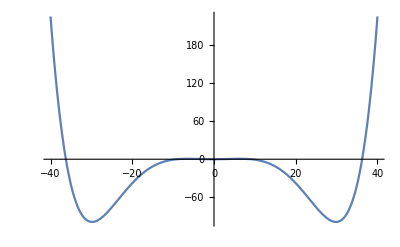

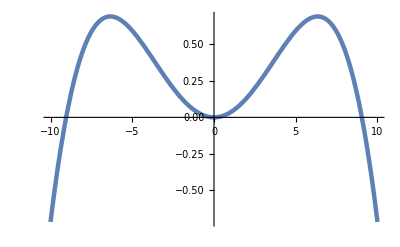

{{W→InterpolatingFunction[{{-50., 50.}, {0., 10.}}, <>]}}

-Graphics3D-

-Graphics3D-

-Graphics3D-

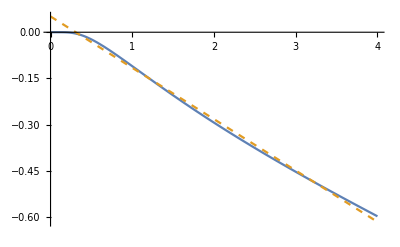

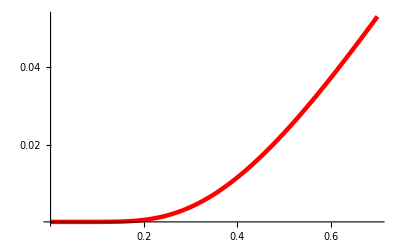

0.166882

```mathematica
kappa = (2 * Pi)* (4.44 +1*0.01)
gamma =(2 * Pi) * (2.30 -1*0.1)
T = 0.02(*temperature in Kelvin*)
aalpha:=(0.51-0.4*0.004) *(kappa + gamma)
Delta =(2 * Pi)* (0.70 -0.3* 0.10)
K = -(2 * Pi)* (0.0002 + 1* 0.00004)
nT = 0.5 * Coth[ 0.319/(2T)] - 0.5
sigmaSP = Sqrt[nT + 1/2]
Qmax = (1/Sqrt[6 Abs[K]])*Sqrt[Delta - Sqrt[aalpha^2 - ((kappa + gamma)/2)^2]]
U[Q_] := (2/(aalpha + (kappa + gamma)/2))* (0.25*( (kappa/2 + gamma/2)^2 + Delta^2 - aalpha^2)* Q^2 + (3/2)* Delta *K* Q^4 + 3 K^2 Q^6) 
Diff = 0.5*(kappa + gamma)*(nT + 1/2)
Plot[U[Q], {Q, -40, 40},LabelStyle -> FontSize ->7,TicksStyle -> Directive[7],PlotRange->All]
Plot[U[Q], {Q, -10, 10},LabelStyle -> FontSize ->12,PlotStyle -> Thickness[0.008], PlotRange->All]
S=NDSolve[{D[W[Q,t],t] == D[W[Q,t],Q]*D[U[Q],Q] +W[Q,t]*D[U[Q],Q,Q]+ Diff * D[W[Q,t],Q,Q], W[Q,0] == (1/(Sqrt[2 Pi] sigmaSP)) Exp[-Q^2/(2 sigmaSP^2)], W[50,t]== 0, W[-50,t]== 0}, W, {Q,-50,50},{t,0,10}]
WW[Q_,t_] :=Evaluate[W[Q,t]/.S] 
Plot3D[WW[Q,t],{Q,-35,-20},{t,0,10},LabelStyle -> FontSize ->12,PlotRange->All]
Plot3D[WW[Q,t],{Q,20,35},{t,0,10},LabelStyle -> FontSize ->12,PlotRange->All]
Plot3D[WW[Q,t],{Q,-6.5,6.5},{t,0,2},LabelStyle -> FontSize ->12,PlotRange->All]
Pdarkleft[t_] := Integrate[WW[Q,t], {Q,-50,-7.5}]
Plot[{Log[1-Pdarkleft[t]],-0.16682(t-0.35) +Log[P[0.35]]},{t,0,4},PlotStyle ->{Directive[color],Directive[Dashed,color]}, LabelStyle -> FontSize ->10]
Plot[Pdarkleft[t], {t,0,0.7},LabelStyle -> FontSize ->16, PlotStyle -> {Red,Thickness[0.008]},Ticks ->{{0.2,0.4, 0.6}, {0.02, 0.04,0.06}}]
-(1/(2-0.228))Log[1-0.256]
```